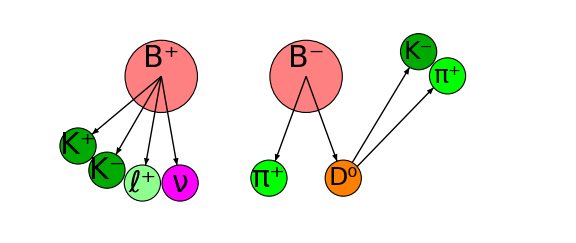

```mathematica
first = {EdgeForm[Black],Pink,
Disk[{0,0},0.2],Disk[{0.8,0},0.2],Black,Text[Style["B^+", FontSize->30,FontFamily->"Palatino Linotype"],{0,0.1}],Text[Style["B^-", FontSize->30,FontFamily->"Palatino Linotype"],{0.8,0.1}]};

second={EdgeForm[Black],
Darker[Green],Disk[RotationMatrix[-140°].{0.6,0},0.1],
Darker[Green],Disk[RotationMatrix[-120°].{0.6,0},0.1],
Lighter[Lighter[Green]],Disk[RotationMatrix[-100°].{0.6,0},0.1],
Magenta,Disk[RotationMatrix[-80°].{0.6,0},0.1],
Black,
Arrow[{{0,0},RotationMatrix[-140°].{0.5,0}}],
Arrow[{{0,0},RotationMatrix[-120°].{0.5,0}}],
Arrow[{{0,0},RotationMatrix[-100°].{0.5,0}}],
Arrow[{{0,0},RotationMatrix[-80°].{0.5,0}}],
Text[Style["K^+", FontSize->30,FontFamily->"Palatino Linotype"],RotationMatrix[-140°].{0.6,0}],
Text[Style["K^-", FontSize->30,FontFamily->"Palatino Linotype"],RotationMatrix[-120°].{0.6,0}],
Text[Style["ℓ^+", FontSize->30,FontFamily->"Palatino Linotype"],RotationMatrix[-100°].{0.6,0}],
Text[Style["ν", FontSize->30,FontFamily->"Palatino Linotype"],RotationMatrix[-80°].{0.6,0}]
};


third={EdgeForm[Black],
Gray,Rotate[Disk[{0.8,0.08}+RotationMatrix[-60°].{0.6,0}-{-0.0,0.03},{0.3,0.1}],Pi/6*0.9],
Black,
Arrow[{{0.8,0},{0.8,0}+RotationMatrix[-40°].{0.5,0}}],
Arrow[{{0.8,0},{0.8,0}+RotationMatrix[-60°].{0.5,0}}],
Arrow[{{0.8,0},{0.8,0}+RotationMatrix[-80°].{0.5,0}}],
Rotate[Text[Style["Generic", FontSize->30,FontFamily->"Palatino Linotype"],{0.8,0.08}+RotationMatrix[-60°].{0.6,0}-{-0.0,0.03}],Pi/6*0.9]
};

third2={EdgeForm[Black],
Gray,Rotate[Disk[{0.8,0.08}+RotationMatrix[-60°].{0.6,0}-{-0.0,0.03},{0.3,0.1}],Pi/6*0.9],
Black,
Arrow[{{0.8,0},{0.8,0}+RotationMatrix[-40°].{0.5,0}}],
Arrow[{{0.8,0},{0.8,0}+RotationMatrix[-60°].{0.5,0}}],
Arrow[{{0.8,0},{0.8,0}+RotationMatrix[-80°].{0.5,0}}],
Red,
Rotate[Text[Style["Generic",FontVariations->{"StrikeThrough"->True}, FontSize->30,FontFamily->"Palatino Linotype"],{0.8,0.08}+RotationMatrix[-60°].{0.6,0}-{-0.0,0.03}],Pi/6*0.9],Black,
Text[Style["*temporary*", FontSize->20,FontFamily->"Palatino Linotype"],{1.5,0.08}]
};

fourth={EdgeForm[{Black,Dashed}],
Orange,Disk[{0.8,0}+RotationMatrix[-70°].{0.6,0},0.1],
Green,Disk[{0.8,0}+RotationMatrix[-110°].{0.6,0},0.1],
Darker[Green],Disk[{0.8,0}+RotationMatrix[-50°].{0.5,0}+RotationMatrix[60°].{0.6,0},0.1],
Green,Disk[{0.8,0}+RotationMatrix[-50°].{0.5,0}+RotationMatrix[40°].{0.6,0},0.1],
Black,
Arrow[{{0.8,0},{0.8,0}+RotationMatrix[-70°].{0.5,0}}],
Arrow[{{0.8,0},{0.8,0}+RotationMatrix[-110°].{0.5,0}}],
Arrow[{{0.8,0}+RotationMatrix[-70°].{0.6,0}+RotationMatrix[60°].{0.1,0},{0.8,0}+RotationMatrix[-50°].{0.5,0}+RotationMatrix[60°].{0.5,0}}],
Arrow[{{0.8,0}+RotationMatrix[-70°].{0.6,0}+RotationMatrix[40°].{0.1,0},{0.8,0}+RotationMatrix[-50°].{0.5,0}+RotationMatrix[40°].{0.5,0}}],
Text[Style["π^+", FontSize->30,FontFamily->"Palatino Linotype"],{0.8,0}+RotationMatrix[-110°].{0.6,0}],
Text[Style["D^0", FontSize->25,FontFamily->"Palatino Linotype"],{0.8,0}+RotationMatrix[-70°].{0.6,0}],
Text[Style["K^-", FontSize->25,FontFamily->"Palatino Linotype"],{0.8,0}+RotationMatrix[-50°].{0.5,0}+RotationMatrix[60°].{0.6,0}],
Text[Style["π^+", FontSize->25,FontFamily->"Palatino Linotype"],{0.8,0}+RotationMatrix[-50°].{0.5,0}+RotationMatrix[40°].{0.6,0}]
};

plot = {{first},{first , second},{first,second,third},{first,second,third2},{first,second,fourth}};

imgplot[k_]:=Graphics[plot[[k]],PlotRange->{{-0.6,2},{-0.8,0.3}},ImageSize->Large]


imgplot[5]
```

```mathematica
Table[Export["/home/mlubej/work/BNote/fig/decay_"<>ToString[i]<>".png",imgplot[i]],{i,{3,5}}]
```

{/home/mlubej/work/BNote/fig/decay_3.png,/home/mlubej/work/BNote/fig/decay_5.png}